```mathematica
(*WALKING KINEMATICS SPEED AND HYPOTHETICAL GAIN STATS PLOTS - Filtered, archived data with LME (from R) lines fitted*)
```

```mathematica
(***********************************************************************************)
(***********************************************************************************)
```

```mathematica
(* Determine operating system *)

os=$OperatingSystem;
frogworkpath="C:\\YOUR FILE DIRECTORY HERE\\" (*Set your main file directory, not to the folder where raw or archived data are stored*)
(*e.g. frogworkpath="C:\\Users\\Documents\\"*)
(*for Mac users change "C:\\" to "\\Volumes\\"*)

dataDirectory="YOUR DIRECTORY TO ARCHIVED .DAT DATA"; (*Set the directory where archived data from the "Code to Archive Data" notebook was exported to*)

setpathDataWin=StringJoin[frogworkpath,dataDirectory];(*windows formatted path as string*)
splitpath=FileNameSplit[setpathDataWin,OperatingSystem->"Windows"(*change to MacOSX if necessary*)];
setpathData=FileNameJoin[splitpath,OperatingSystem->os];
SetDirectory[setpathData];

(***********************************************************************************)

(* Determine animal filename *)

Needs["GraphUtilities`"]
whatFrog[filename_]:=StringTake[filename,{3,4}](*extracts the animal number*)
trialFiles=FileNames[];
ntrials=Length[trialFiles];
trialMatrix=GatherBy[trialFiles,whatFrog];(*organize the trials in a matrix *)
ExpressionTreePlot[trialMatrix,VertexLabeling->Tooltip];

(******************************************************************************************)

(*INPUT - Type Animal Filename *)
(*DOESN'T MATTER WHICH ONE CHOSEN*)

animalfilename=trialMatrix[[1,1]]; (*DO NOT CHANGE THIS TRIAL MATRIX!!!*)

(******************************************************************************************)

(* Import raw data *)

allrawtrialdata=Import[animalfilename,"Data"];

(***********************************************************************************)

(* Import metadata*)
(*Set the directory where the METADATA.xlsx is saved*)

(*SET DIRECTORY*)
dataDirectory="YOUR DIRECTORY TO METADATA.xlsx FILE";

setpathDataWin=StringJoin[frogworkpath,dataDirectory];(*windows formatted path as string*)
splitpath=FileNameSplit[setpathDataWin,OperatingSystem->"Windows"(*change to MacOSX if necessary*)];
setpathData=FileNameJoin[splitpath,OperatingSystem->os];
SetDirectory[setpathData];

importedmetadata=Import["METADATA.xlsx","Data"];
metadata=importedmetadata[[1,2;;24,All]];

(***********************************************************************************)

(* Metadata file map: Locate information *)

Framerate=metadata[[1,3]];
```

```mathematica
(***********************************************************************************)

(*Speed*)
dataDirectory="YOUR DIRECTORY FOR SPEED DATA";

setpathDataWin=StringJoin[frogworkpath,dataDirectory];(*windows formatted path as string*)
splitpath=FileNameSplit[setpathDataWin,OperatingSystem->"Windows"(*change to MacOSX if necessary*)];
setpathData=FileNameJoin[splitpath,OperatingSystem->os];
SetDirectory[setpathData];

(*IMPORT SPEED DATA*)

Animal0Trial1Speeddata=Import["KM01_RUN_02_Speed of single limb cycle.xlsx","Data"];
Animal1Trial1Speeddata=Import["KM02_RUN_01_Speed of single limb cycle.xlsx","Data"];
Animal1Trial2Speeddata=Import["KM02_RUN_02_Speed of single limb cycle.xlsx","Data"];
Animal1Trial3Speeddata=Import["KM02_RUN_09_Speed of single limb cycle.xlsx","Data"];
Animal2Trial1Speeddata=Import["KM04_RUN_09_Speed of single limb cycle.xlsx","Data"];
Animal2Trial2Speeddata=Import["KM04_RUN_11_Speed of single limb cycle.xlsx","Data"];
Animal2Trial3Speeddata=Import["KM04_RUN_12_Speed of single limb cycle.xlsx","Data"];
Animal3Trial1Speeddata=Import["KM05_RUN_04_Speed of single limb cycle.xlsx","Data"];
Animal3Trial2Speeddata=Import["KM05_RUN_08_Speed of single limb cycle.xlsx","Data"];
Animal4Trial1Speeddata=Import["KM06_RUN_11_Speed of single limb cycle.xlsx","Data"];
Animal4Trial2Speeddata=Import["KM06_RUN_12_Speed of single limb cycle.xlsx","Data"];
Animal4Trial3Speeddata=Import["KM06_RUN_13_Speed of single limb cycle.xlsx","Data"];
Animal4Trial4Speeddata=Import["KM06_RUN_15_Speed of single limb cycle.xlsx","Data"];
Animal4Trial5Speeddata=Import["KM06_RUN_16_Speed of single limb cycle.xlsx","Data"];
Animal5Trial1Speeddata=Import["KM07_RUN_14_Speed of single limb cycle.xlsx","Data"];
Animal5Trial2Speeddata=Import["KM07_RUN_16_Speed of single limb cycle.xlsx","Data"];
Animal5Trial3Speeddata=Import["KM07_RUN_17_Speed of single limb cycle.xlsx","Data"];
Animal6Trial1Speeddata=Import["KM08_RUN_09_Speed of single limb cycle.xlsx","Data"];
Animal6Trial2Speeddata=Import["KM08_RUN_10_Speed of single limb cycle.xlsx","Data"];
Animal7Trial1Speeddata=Import["KM23_RUN_01_Speed of single limb cycle.xlsx","Data"];
Animal7Trial2Speeddata=Import["KM23_RUN_02_Speed of single limb cycle.xlsx","Data"];
Animal7Trial3Speeddata=Import["KM23_RUN_03_Speed of single limb cycle.xlsx","Data"];
Animal7Trial4Speeddata=Import["KM23_RUN_05_Speed of single limb cycle.xlsx","Data"];

Animal0Trial1Speed=Flatten[Animal0Trial1Speeddata[[1]]];
Animal1Trial1Speed=Flatten[Animal1Trial1Speeddata[[1]]];
Animal1Trial2Speed=Flatten[Animal1Trial2Speeddata[[1]]];
Animal1Trial3Speed=Flatten[Animal1Trial3Speeddata[[1]]];
Animal2Trial1Speed=Flatten[Animal2Trial1Speeddata[[1]]];
Animal2Trial2Speed=Flatten[Animal2Trial2Speeddata[[1]]];
Animal2Trial3Speed=Flatten[Animal2Trial3Speeddata[[1]]];
Animal3Trial1Speed=Flatten[Animal3Trial1Speeddata[[1]]];
Animal3Trial2Speed=Flatten[Animal3Trial2Speeddata[[1]]];
Animal4Trial1Speed=Flatten[Animal4Trial1Speeddata[[1]]];
Animal4Trial2Speed=Flatten[Animal4Trial2Speeddata[[1]]];
Animal4Trial3Speed=Flatten[Animal4Trial3Speeddata[[1]]];
Animal4Trial4Speed=Flatten[Animal4Trial4Speeddata[[1]]];
Animal4Trial5Speed=Flatten[Animal4Trial5Speeddata[[1]]];
Animal5Trial1Speed=Flatten[Animal5Trial1Speeddata[[1]]];
Animal5Trial2Speed=Flatten[Animal5Trial2Speeddata[[1]]];
Animal5Trial3Speed=Flatten[Animal5Trial3Speeddata[[1]]];
Animal6Trial1Speed=Flatten[Animal6Trial1Speeddata[[1]]];
Animal6Trial2Speed=Flatten[Animal6Trial2Speeddata[[1]]];
Animal7Trial1Speed=Flatten[Animal7Trial1Speeddata[[1]]];
Animal7Trial2Speed=Flatten[Animal7Trial2Speeddata[[1]]];
Animal7Trial3Speed=Flatten[Animal7Trial3Speeddata[[1]]];
Animal7Trial4Speed=Flatten[Animal7Trial4Speeddata[[1]]];
Dimensions[Animal1Trial1Speed];


Animal0Speeds=Join[Animal0Trial1Speed];
Animal1Speeds=Join[Animal1Trial1Speed,Animal1Trial2Speed,Animal1Trial3Speed];
Animal2Speeds=Join[Animal2Trial1Speed,Animal2Trial2Speed,Animal2Trial3Speed];
Animal3Speeds=Join[Animal3Trial1Speed,Animal3Trial2Speed];
Animal4Speeds=Join[Animal4Trial1Speed,Animal4Trial2Speed,Animal4Trial3Speed,Animal4Trial4Speed,Animal4Trial5Speed];
Animal5Speeds=Join[Animal5Trial1Speed,Animal5Trial2Speed,Animal5Trial3Speed];
Animal6Speeds=Join[Animal6Trial1Speed,Animal6Trial2Speed];
Animal7Speeds=Join[Animal7Trial1Speed,Animal7Trial2Speed,Animal7Trial3Speed,Animal7Trial4Speed];

TrialSpeedAllAnimals=Join[Animal0Trial1Speed,Animal1Trial1Speed,Animal1Trial2Speed,Animal1Trial3Speed,Animal2Trial1Speed,Animal2Trial2Speed,Animal2Trial3Speed,Animal3Trial1Speed,Animal3Trial2Speed,Animal4Trial1Speed,Animal4Trial2Speed,Animal4Trial3Speed,Animal4Trial4Speed,Animal4Trial5Speed,Animal5Trial1Speed,Animal5Trial2Speed,Animal5Trial3Speed,Animal6Trial1Speed,Animal6Trial2Speed,Animal7Trial1Speed,Animal7Trial2Speed,Animal7Trial3Speed,Animal7Trial4Speed]
Dimensions[TrialSpeedAllAnimals];
```

{0.519411,1.32091,0.815714,1.13333,1.31853,1.39296,1.71705,1.62011,2.17293,1.90285,2.59809,1.60639,2.15418,1.88545,4.26555,3.52822,4.98496,2.3893,1.53747,4.4425,3.06853,3.80005,1.26247}

```mathematica
(***********************************************************************************)

(*Pelvic excursion*)
dataDirectory="YOUR DIRECTORY FOR PELVIC ANGLE EXCURSION DATA";

setpathDataWin=StringJoin[frogworkpath,dataDirectory];(*windows formatted path as string*)
splitpath=FileNameSplit[setpathDataWin,OperatingSystem->"Windows"(*change to MacOSX if necessary*)];
setpathData=FileNameJoin[splitpath,OperatingSystem->os];
SetDirectory[setpathData];

(*IMPORT PELVIC ANGULAR EXCURSION DATA*)

Animal0Trial1PAEdata=Import["KM01_RUN_02_Total Pelvic Vector Angular Excursion - One Limb Cycle - FILTERED.xlsx","Data"];
Animal1Trial1PAEdata=Import["KM02_RUN_01_Total Pelvic Vector Angular Excursion - One Limb Cycle - FILTERED.xlsx","Data"];
Animal1Trial2PAEdata=Import["KM02_RUN_02_Total Pelvic Vector Angular Excursion - One Limb Cycle - FILTERED.xlsx","Data"];
Animal1Trial3PAEdata=Import["KM02_RUN_09_Total Pelvic Vector Angular Excursion - One Limb Cycle - FILTERED.xlsx","Data"];
Animal2Trial1PAEdata=Import["KM04_RUN_09_Total Pelvic Vector Angular Excursion - One Limb Cycle - FILTERED.xlsx","Data"];
Animal2Trial2PAEdata=Import["KM04_RUN_11_Total Pelvic Vector Angular Excursion - One Limb Cycle - FILTERED.xlsx","Data"];
Animal2Trial3PAEdata=Import["KM04_RUN_12_Total Pelvic Vector Angular Excursion - One Limb Cycle - FILTERED.xlsx","Data"];
Animal3Trial1PAEdata=Import["KM05_RUN_04_Total Pelvic Vector Angular Excursion - One Limb Cycle - FILTERED.xlsx","Data"];
Animal3Trial2PAEdata=Import["KM05_RUN_08_Total Pelvic Vector Angular Excursion - One Limb Cycle - FILTERED.xlsx","Data"];
Animal4Trial1PAEdata=Import["KM06_RUN_11_Total Pelvic Vector Angular Excursion - One Limb Cycle - FILTERED.xlsx","Data"];
Animal4Trial2PAEdata=Import["KM06_RUN_12_Total Pelvic Vector Angular Excursion - One Limb Cycle - FILTERED.xlsx","Data"];
Animal4Trial3PAEdata=Import["KM06_RUN_13_Total Pelvic Vector Angular Excursion - One Limb Cycle - FILTERED.xlsx","Data"];
Animal4Trial4PAEdata=Import["KM06_RUN_15_Total Pelvic Vector Angular Excursion - One Limb Cycle - FILTERED.xlsx","Data"];
Animal4Trial5PAEdata=Import["KM06_RUN_16_Total Pelvic Vector Angular Excursion - One Limb Cycle - FILTERED.xlsx","Data"];
Animal5Trial1PAEdata=Import["KM07_RUN_14_Total Pelvic Vector Angular Excursion - One Limb Cycle - FILTERED.xlsx","Data"];
Animal5Trial2PAEdata=Import["KM07_RUN_16_Total Pelvic Vector Angular Excursion - One Limb Cycle - FILTERED.xlsx","Data"];
Animal5Trial3PAEdata=Import["KM07_RUN_17_Total Pelvic Vector Angular Excursion - One Limb Cycle - FILTERED.xlsx","Data"];
Animal6Trial1PAEdata=Import["KM08_RUN_09_Total Pelvic Vector Angular Excursion - One Limb Cycle - FILTERED.xlsx","Data"];
Animal6Trial2PAEdata=Import["KM08_RUN_10_Total Pelvic Vector Angular Excursion - One Limb Cycle - FILTERED.xlsx","Data"];
Animal7Trial1PAEdata=Import["KM23_RUN_01_Total Pelvic Vector Angular Excursion - One Limb Cycle - FILTERED.xlsx","Data"];
Animal7Trial2PAEdata=Import["KM23_RUN_02_Total Pelvic Vector Angular Excursion - One Limb Cycle - FILTERED.xlsx","Data"];
Animal7Trial3PAEdata=Import["KM23_RUN_03_Total Pelvic Vector Angular Excursion - One Limb Cycle - FILTERED.xlsx","Data"];
Animal7Trial4PAEdata=Import["KM23_RUN_05_Total Pelvic Vector Angular Excursion - One Limb Cycle - FILTERED.xlsx","Data"];

Animal0Trial1PAE=Flatten[Animal0Trial1PAEdata[[1]]];
Animal1Trial1PAE=Flatten[Animal1Trial1PAEdata[[1]]];
Animal1Trial2PAE=Flatten[Animal1Trial2PAEdata[[1]]];
Animal1Trial3PAE=Flatten[Animal1Trial3PAEdata[[1]]];
Animal2Trial1PAE=Flatten[Animal2Trial1PAEdata[[1]]];
Animal2Trial2PAE=Flatten[Animal2Trial2PAEdata[[1]]];
Animal2Trial3PAE=Flatten[Animal2Trial3PAEdata[[1]]];
Animal3Trial1PAE=Flatten[Animal3Trial1PAEdata[[1]]];
Animal3Trial2PAE=Flatten[Animal3Trial2PAEdata[[1]]];
Animal4Trial1PAE=Flatten[Animal4Trial1PAEdata[[1]]];
Animal4Trial2PAE=Flatten[Animal4Trial2PAEdata[[1]]];
Animal4Trial3PAE=Flatten[Animal4Trial3PAEdata[[1]]];
Animal4Trial4PAE=Flatten[Animal4Trial4PAEdata[[1]]];
Animal4Trial5PAE=Flatten[Animal4Trial5PAEdata[[1]]];
Animal5Trial1PAE=Flatten[Animal5Trial1PAEdata[[1]]];
Animal5Trial2PAE=Flatten[Animal5Trial2PAEdata[[1]]];
Animal5Trial3PAE=Flatten[Animal5Trial3PAEdata[[1]]];
Animal6Trial1PAE=Flatten[Animal6Trial1PAEdata[[1]]];
Animal6Trial2PAE=Flatten[Animal6Trial2PAEdata[[1]]];
Animal7Trial1PAE=Flatten[Animal7Trial1PAEdata[[1]]];
Animal7Trial2PAE=Flatten[Animal7Trial2PAEdata[[1]]];
Animal7Trial3PAE=Flatten[Animal7Trial3PAEdata[[1]]];
Animal7Trial4PAE=Flatten[Animal7Trial4PAEdata[[1]]];
Dimensions[Animal1Trial1PAE];

Animal0PelvicAngularExcursions=Join[Animal0Trial1PAE];
Animal1PelvicAngularExcursions=Join[Animal1Trial1PAE,Animal1Trial2PAE,Animal1Trial3PAE];
Animal2PelvicAngularExcursions=Join[Animal2Trial1PAE,Animal2Trial2PAE,Animal2Trial3PAE];
Animal3PelvicAngularExcursions=Join[Animal3Trial1PAE,Animal3Trial2PAE];
Animal4PelvicAngularExcursions=Join[Animal4Trial1PAE,Animal4Trial2PAE,Animal4Trial3PAE,Animal4Trial4PAE,Animal4Trial5PAE];
Animal5PelvicAngularExcursions=Join[Animal5Trial1PAE,Animal5Trial2PAE,Animal5Trial3PAE];
Animal6PelvicAngularExcursions=Join[Animal6Trial1PAE,Animal6Trial2PAE];
Animal7PelvicAngularExcursions=Join[Animal7Trial1PAE,Animal7Trial2PAE,Animal7Trial3PAE,Animal7Trial4PAE];

PelvicAngularExcursionAllAnimals=Join[Animal0Trial1PAE,Animal1Trial1PAE,Animal1Trial2PAE,Animal1Trial3PAE,Animal2Trial1PAE,Animal2Trial2PAE,Animal2Trial3PAE,Animal3Trial1PAE,Animal3Trial2PAE,Animal4Trial1PAE,Animal4Trial2PAE,Animal4Trial3PAE,Animal4Trial4PAE,Animal4Trial5PAE,Animal5Trial1PAE,Animal5Trial2PAE,Animal5Trial3PAE,Animal6Trial1PAE,Animal6Trial2PAE,Animal7Trial1PAE,Animal7Trial2PAE,Animal7Trial3PAE,Animal7Trial4PAE]
Dimensions[PelvicAngularExcursionAllAnimals];
```

{16.1611,17.583,13.5309,14.7144,20.9355,16.5536,15.6786,14.2711,11.3032,13.2846,8.63345,11.3837,11.8961,12.7532,5.77536,5.03916,4.30451,14.3282,16.1793,7.18852,18.1348,13.9318,8.65496}

```mathematica
(***********************************************************************************)

(*fore-aft excursions*)
dataDirectory="YOUR DIRECTORY FOR JOINT DISTANCE TRAVELLED DATA";

setpathDataWin=StringJoin[frogworkpath,dataDirectory];(*windows formatted path as string*)
splitpath=FileNameSplit[setpathDataWin,OperatingSystem->"Windows"(*change to MacOSX if necessary*)];
setpathData=FileNameJoin[splitpath,OperatingSystem->os];
SetDirectory[setpathData];

(*IMPORT TMT DISTANCE TRAVELLED DATA*)

Animal0Trial1TMTEdata=Import["KM01_RUN_02_TMT distance travelled - Model 1 Fixed body axis.xlsx","Data"];
Animal1Trial1TMTEdata=Import["KM02_RUN_01_TMT distance travelled - Model 1 Fixed body axis.xlsx","Data"];
Animal1Trial2TMTEdata=Import["KM02_RUN_02_TMT distance travelled - Model 1 Fixed body axis.xlsx","Data"];
Animal1Trial3TMTEdata=Import["KM02_RUN_09_TMT distance travelled - Model 1 Fixed body axis.xlsx","Data"];
Animal2Trial1TMTEdata=Import["KM04_RUN_09_TMT distance travelled - Model 1 Fixed body axis.xlsx","Data"];
Animal2Trial2TMTEdata=Import["KM04_RUN_11_TMT distance travelled - Model 1 Fixed body axis.xlsx","Data"];
Animal2Trial3TMTEdata=Import["KM04_RUN_12_TMT distance travelled - Model 1 Fixed body axis.xlsx","Data"];
Animal3Trial1TMTEdata=Import["KM05_RUN_04_TMT distance travelled - Model 1 Fixed body axis.xlsx","Data"];
Animal3Trial2TMTEdata=Import["KM05_RUN_08_TMT distance travelled - Model 1 Fixed body axis.xlsx","Data"];
Animal4Trial1TMTEdata=Import["KM06_RUN_11_TMT distance travelled - Model 1 Fixed body axis.xlsx","Data"];
Animal4Trial2TMTEdata=Import["KM06_RUN_12_TMT distance travelled - Model 1 Fixed body axis.xlsx","Data"];
Animal4Trial3TMTEdata=Import["KM06_RUN_13_TMT distance travelled - Model 1 Fixed body axis.xlsx","Data"];
Animal4Trial4TMTEdata=Import["KM06_RUN_15_TMT distance travelled - Model 1 Fixed body axis.xlsx","Data"];
Animal4Trial5TMTEdata=Import["KM06_RUN_16_TMT distance travelled - Model 1 Fixed body axis.xlsx","Data"];
Animal5Trial1TMTEdata=Import["KM07_RUN_14_TMT distance travelled - Model 1 Fixed body axis.xlsx","Data"];
Animal5Trial2TMTEdata=Import["KM07_RUN_16_TMT distance travelled - Model 1 Fixed body axis.xlsx","Data"];
Animal5Trial3TMTEdata=Import["KM07_RUN_17_TMT distance travelled - Model 1 Fixed body axis.xlsx","Data"];
Animal6Trial1TMTEdata=Import["KM08_RUN_09_TMT distance travelled - Model 1 Fixed body axis.xlsx","Data"];
Animal6Trial2TMTEdata=Import["KM08_RUN_10_TMT distance travelled - Model 1 Fixed body axis.xlsx","Data"];
Animal7Trial1TMTEdata=Import["KM23_RUN_01_TMT distance travelled - Model 1 Fixed body axis.xlsx","Data"];
Animal7Trial2TMTEdata=Import["KM23_RUN_02_TMT distance travelled - Model 1 Fixed body axis.xlsx","Data"];
Animal7Trial3TMTEdata=Import["KM23_RUN_03_TMT distance travelled - Model 1 Fixed body axis.xlsx","Data"];
Animal7Trial4TMTEdata=Import["KM23_RUN_05_TMT distance travelled - Model 1 Fixed body axis.xlsx","Data"];

Animal0Trial1TMTE=Flatten[Animal0Trial1TMTEdata[[1]]];
Animal1Trial1TMTE=Flatten[Animal1Trial1TMTEdata[[1]]];
Animal1Trial2TMTE=Flatten[Animal1Trial2TMTEdata[[1]]];
Animal1Trial3TMTE=Flatten[Animal1Trial3TMTEdata[[1]]];
Animal2Trial1TMTE=Flatten[Animal2Trial1TMTEdata[[1]]];
Animal2Trial2TMTE=Flatten[Animal2Trial2TMTEdata[[1]]];
Animal2Trial3TMTE=Flatten[Animal2Trial3TMTEdata[[1]]];
Animal3Trial1TMTE=Flatten[Animal3Trial1TMTEdata[[1]]];
Animal3Trial2TMTE=Flatten[Animal3Trial2TMTEdata[[1]]];
Animal4Trial1TMTE=Flatten[Animal4Trial1TMTEdata[[1]]];
Animal4Trial2TMTE=Flatten[Animal4Trial2TMTEdata[[1]]];
Animal4Trial3TMTE=Flatten[Animal4Trial3TMTEdata[[1]]];
Animal4Trial4TMTE=Flatten[Animal4Trial4TMTEdata[[1]]];
Animal4Trial5TMTE=Flatten[Animal4Trial5TMTEdata[[1]]];
Animal5Trial1TMTE=Flatten[Animal5Trial1TMTEdata[[1]]];
Animal5Trial2TMTE=Flatten[Animal5Trial2TMTEdata[[1]]];
Animal5Trial3TMTE=Flatten[Animal5Trial3TMTEdata[[1]]];
Animal6Trial1TMTE=Flatten[Animal6Trial1TMTEdata[[1]]];
Animal6Trial2TMTE=Flatten[Animal6Trial2TMTEdata[[1]]];
Animal7Trial1TMTE=Flatten[Animal7Trial1TMTEdata[[1]]];
Animal7Trial2TMTE=Flatten[Animal7Trial2TMTEdata[[1]]];
Animal7Trial3TMTE=Flatten[Animal7Trial3TMTEdata[[1]]];
Animal7Trial4TMTE=Flatten[Animal7Trial4TMTEdata[[1]]];
Dimensions[Animal1Trial1TMTE];

Animal0TMTforeaftExcursions=Join[Animal0Trial1TMTE];
Animal1TMTforeaftExcursions=Join[Animal1Trial1TMTE,Animal1Trial2TMTE,Animal1Trial3TMTE];
Animal2TMTforeaftExcursions=Join[Animal2Trial1TMTE,Animal2Trial2TMTE,Animal2Trial3TMTE];
Animal3TMTforeaftExcursions=Join[Animal3Trial1TMTE,Animal3Trial2TMTE];
Animal4TMTforeaftExcursions=Join[Animal4Trial1TMTE,Animal4Trial2TMTE,Animal4Trial3TMTE,Animal4Trial4TMTE,Animal4Trial5TMTE];
Animal5TMTforeaftExcursions=Join[Animal5Trial1TMTE,Animal5Trial2TMTE,Animal5Trial3TMTE];
Animal6TMTforeaftExcursions=Join[Animal6Trial1TMTE,Animal6Trial2TMTE];
Animal7TMTforeaftExcursions=Join[Animal7Trial1TMTE,Animal7Trial2TMTE,Animal7Trial3TMTE,Animal7Trial4TMTE];

TMTforeaftExcursionAllAnimals=Join[Animal0Trial1TMTE,Animal1Trial1TMTE,Animal1Trial2TMTE,Animal1Trial3TMTE,Animal2Trial1TMTE,Animal2Trial2TMTE,Animal2Trial3TMTE,Animal3Trial1TMTE,Animal3Trial2TMTE,Animal4Trial1TMTE,Animal4Trial2TMTE,Animal4Trial3TMTE,Animal4Trial4TMTE,Animal4Trial5TMTE,Animal5Trial1TMTE,Animal5Trial2TMTE,Animal5Trial3TMTE,Animal6Trial1TMTE,Animal6Trial2TMTE,Animal7Trial1TMTE,Animal7Trial2TMTE,Animal7Trial3TMTE,Animal7Trial4TMTE]
Dimensions[TMTforeaftExcursionAllAnimals];

(*IMPORT ANK DISTANCE TRAVELLED DATA*)

Animal0Trial1ANKEdata=Import["KM01_RUN_02_Ankle distance travelled - Model 1 Fixed body axis.xlsx","Data"];
Animal1Trial1ANKEdata=Import["KM02_RUN_01_Ankle distance travelled - Model 1 Fixed body axis.xlsx","Data"];
Animal1Trial2ANKEdata=Import["KM02_RUN_02_Ankle distance travelled - Model 1 Fixed body axis.xlsx","Data"];
Animal1Trial3ANKEdata=Import["KM02_RUN_09_Ankle distance travelled - Model 1 Fixed body axis.xlsx","Data"];
Animal2Trial1ANKEdata=Import["KM04_RUN_09_Ankle distance travelled - Model 1 Fixed body axis.xlsx","Data"];
Animal2Trial2ANKEdata=Import["KM04_RUN_11_Ankle distance travelled - Model 1 Fixed body axis.xlsx","Data"];
Animal2Trial3ANKEdata=Import["KM04_RUN_12_Ankle distance travelled - Model 1 Fixed body axis.xlsx","Data"];
Animal3Trial1ANKEdata=Import["KM05_RUN_04_Ankle distance travelled - Model 1 Fixed body axis.xlsx","Data"];
Animal3Trial2ANKEdata=Import["KM05_RUN_08_Ankle distance travelled - Model 1 Fixed body axis.xlsx","Data"];
Animal4Trial1ANKEdata=Import["KM06_RUN_11_Ankle distance travelled - Model 1 Fixed body axis.xlsx","Data"];
Animal4Trial2ANKEdata=Import["KM06_RUN_12_Ankle distance travelled - Model 1 Fixed body axis.xlsx","Data"];
Animal4Trial3ANKEdata=Import["KM06_RUN_13_Ankle distance travelled - Model 1 Fixed body axis.xlsx","Data"];
Animal4Trial4ANKEdata=Import["KM06_RUN_15_Ankle distance travelled - Model 1 Fixed body axis.xlsx","Data"];
Animal4Trial5ANKEdata=Import["KM06_RUN_16_Ankle distance travelled - Model 1 Fixed body axis.xlsx","Data"];
Animal5Trial1ANKEdata=Import["KM07_RUN_14_Ankle distance travelled - Model 1 Fixed body axis.xlsx","Data"];
Animal5Trial2ANKEdata=Import["KM07_RUN_16_Ankle distance travelled - Model 1 Fixed body axis.xlsx","Data"];
Animal5Trial3ANKEdata=Import["KM07_RUN_17_Ankle distance travelled - Model 1 Fixed body axis.xlsx","Data"];
Animal6Trial1ANKEdata=Import["KM08_RUN_09_Ankle distance travelled - Model 1 Fixed body axis.xlsx","Data"];
Animal6Trial2ANKEdata=Import["KM08_RUN_10_Ankle distance travelled - Model 1 Fixed body axis.xlsx","Data"];
Animal7Trial1ANKEdata=Import["KM23_RUN_01_Ankle distance travelled - Model 1 Fixed body axis.xlsx","Data"];
Animal7Trial2ANKEdata=Import["KM23_RUN_02_Ankle distance travelled - Model 1 Fixed body axis.xlsx","Data"];Animal7Trial3ANKEdata=Import["KM23_RUN_03_Ankle distance travelled - Model 1 Fixed body axis.xlsx","Data"];
Animal7Trial4ANKEdata=Import["KM23_RUN_05_Ankle distance travelled - Model 1 Fixed body axis.xlsx","Data"];

Animal0Trial1ANKE=Flatten[Animal0Trial1ANKEdata[[1]]];
Animal1Trial1ANKE=Flatten[Animal1Trial1ANKEdata[[1]]];
Animal1Trial2ANKE=Flatten[Animal1Trial2ANKEdata[[1]]];
Animal1Trial3ANKE=Flatten[Animal1Trial3ANKEdata[[1]]];
Animal2Trial1ANKE=Flatten[Animal2Trial1ANKEdata[[1]]];
Animal2Trial2ANKE=Flatten[Animal2Trial2ANKEdata[[1]]];
Animal2Trial3ANKE=Flatten[Animal2Trial3ANKEdata[[1]]];
Animal3Trial1ANKE=Flatten[Animal3Trial1ANKEdata[[1]]];
Animal3Trial2ANKE=Flatten[Animal3Trial2ANKEdata[[1]]];
Animal4Trial1ANKE=Flatten[Animal4Trial1ANKEdata[[1]]];
Animal4Trial2ANKE=Flatten[Animal4Trial2ANKEdata[[1]]];
Animal4Trial3ANKE=Flatten[Animal4Trial3ANKEdata[[1]]];
Animal4Trial4ANKE=Flatten[Animal4Trial4ANKEdata[[1]]];
Animal4Trial5ANKE=Flatten[Animal4Trial5ANKEdata[[1]]];
Animal5Trial1ANKE=Flatten[Animal5Trial1ANKEdata[[1]]];
Animal5Trial2ANKE=Flatten[Animal5Trial2ANKEdata[[1]]];
Animal5Trial3ANKE=Flatten[Animal5Trial3ANKEdata[[1]]];
Animal6Trial1ANKE=Flatten[Animal6Trial1ANKEdata[[1]]];
Animal6Trial2ANKE=Flatten[Animal6Trial2ANKEdata[[1]]];
Animal7Trial1ANKE=Flatten[Animal7Trial1ANKEdata[[1]]];
Animal7Trial2ANKE=Flatten[Animal7Trial2ANKEdata[[1]]];
Animal7Trial3ANKE=Flatten[Animal7Trial3ANKEdata[[1]]];
Animal7Trial4ANKE=Flatten[Animal7Trial4ANKEdata[[1]]];
Dimensions[Animal1Trial1ANKE];

Animal0ANKforeaftExcursions=Join[Animal0Trial1ANKE];
Animal1ANKforeaftExcursions=Join[Animal1Trial1ANKE,Animal1Trial2ANKE,Animal1Trial3ANKE];
Animal2ANKforeaftExcursions=Join[Animal2Trial1ANKE,Animal2Trial2ANKE,Animal2Trial3ANKE];
Animal3ANKforeaftExcursions=Join[Animal3Trial1ANKE,Animal3Trial2ANKE];
Animal4ANKforeaftExcursions=Join[Animal4Trial1ANKE,Animal4Trial2ANKE,Animal4Trial3ANKE,Animal4Trial4ANKE,Animal4Trial5ANKE];
Animal5ANKforeaftExcursions=Join[Animal5Trial1ANKE,Animal5Trial2ANKE,Animal5Trial3ANKE];
Animal6ANKforeaftExcursions=Join[Animal6Trial1ANKE,Animal6Trial2ANKE];
Animal7ANKforeaftExcursions=Join[Animal7Trial1ANKE,Animal7Trial2ANKE,Animal7Trial3ANKE,Animal7Trial4ANKE];

ANKforeaftExcursionAllAnimals=Join[Animal0Trial1ANKE,Animal1Trial1ANKE,Animal1Trial2ANKE,Animal1Trial3ANKE,Animal2Trial1ANKE,Animal2Trial2ANKE,Animal2Trial3ANKE,Animal3Trial1ANKE,Animal3Trial2ANKE,Animal4Trial1ANKE,Animal4Trial2ANKE,Animal4Trial3ANKE,Animal4Trial4ANKE,Animal4Trial5ANKE,Animal5Trial1ANKE,Animal5Trial2ANKE,Animal5Trial3ANKE,Animal6Trial1ANKE,Animal6Trial2ANKE,Animal7Trial1ANKE,Animal7Trial2ANKE,Animal7Trial3ANKE,Animal7Trial4ANKE]
Dimensions[ANKforeaftExcursionAllAnimals];


(*IMPORT KNE DISTANCE TRAVELLED DATA*)

Animal0Trial1KNEEdata=Import["KM01_RUN_02_Knee distance travelled - Model 1 Fixed body axis.xlsx","Data"];
Animal1Trial1KNEEdata=Import["KM02_RUN_01_Knee distance travelled - Model 1 Fixed body axis.xlsx","Data"];
Animal1Trial2KNEEdata=Import["KM02_RUN_02_Knee distance travelled - Model 1 Fixed body axis.xlsx","Data"];
Animal1Trial3KNEEdata=Import["KM02_RUN_09_Knee distance travelled - Model 1 Fixed body axis.xlsx","Data"];
Animal2Trial1KNEEdata=Import["KM04_RUN_09_Knee distance travelled - Model 1 Fixed body axis.xlsx","Data"];
Animal2Trial2KNEEdata=Import["KM04_RUN_11_Knee distance travelled - Model 1 Fixed body axis.xlsx","Data"];
Animal2Trial3KNEEdata=Import["KM04_RUN_12_Knee distance travelled - Model 1 Fixed body axis.xlsx","Data"];
Animal3Trial1KNEEdata=Import["KM05_RUN_04_Knee distance travelled - Model 1 Fixed body axis.xlsx","Data"];
Animal3Trial2KNEEdata=Import["KM05_RUN_08_Knee distance travelled - Model 1 Fixed body axis.xlsx","Data"];
Animal4Trial1KNEEdata=Import["KM06_RUN_11_Knee distance travelled - Model 1 Fixed body axis.xlsx","Data"];
Animal4Trial2KNEEdata=Import["KM06_RUN_12_Knee distance travelled - Model 1 Fixed body axis.xlsx","Data"];
Animal4Trial3KNEEdata=Import["KM06_RUN_13_Knee distance travelled - Model 1 Fixed body axis.xlsx","Data"];
Animal4Trial4KNEEdata=Import["KM06_RUN_15_Knee distance travelled - Model 1 Fixed body axis.xlsx","Data"];
Animal4Trial5KNEEdata=Import["KM06_RUN_16_Knee distance travelled - Model 1 Fixed body axis.xlsx","Data"];
Animal5Trial1KNEEdata=Import["KM07_RUN_14_Knee distance travelled - Model 1 Fixed body axis.xlsx","Data"];
Animal5Trial2KNEEdata=Import["KM07_RUN_16_Knee distance travelled - Model 1 Fixed body axis.xlsx","Data"];
Animal5Trial3KNEEdata=Import["KM07_RUN_17_Knee distance travelled - Model 1 Fixed body axis.xlsx","Data"];
Animal6Trial1KNEEdata=Import["KM08_RUN_09_Knee distance travelled - Model 1 Fixed body axis.xlsx","Data"];
Animal6Trial2KNEEdata=Import["KM08_RUN_10_Knee distance travelled - Model 1 Fixed body axis.xlsx","Data"];
Animal7Trial1KNEEdata=Import["KM23_RUN_01_Knee distance travelled - Model 1 Fixed body axis.xlsx","Data"];
Animal7Trial2KNEEdata=Import["KM23_RUN_02_Knee distance travelled - Model 1 Fixed body axis.xlsx","Data"];
Animal7Trial3KNEEdata=Import["KM23_RUN_03_Knee distance travelled - Model 1 Fixed body axis.xlsx","Data"];
Animal7Trial4KNEEdata=Import["KM23_RUN_05_Knee distance travelled - Model 1 Fixed body axis.xlsx","Data"];

Animal0Trial1KNEE=Flatten[Animal0Trial1KNEEdata[[1]]];
Animal1Trial1KNEE=Flatten[Animal1Trial1KNEEdata[[1]]];
Animal1Trial2KNEE=Flatten[Animal1Trial2KNEEdata[[1]]];
Animal1Trial3KNEE=Flatten[Animal1Trial3KNEEdata[[1]]];
Animal2Trial1KNEE=Flatten[Animal2Trial1KNEEdata[[1]]];
Animal2Trial2KNEE=Flatten[Animal2Trial2KNEEdata[[1]]];
Animal2Trial3KNEE=Flatten[Animal2Trial3KNEEdata[[1]]];
Animal3Trial1KNEE=Flatten[Animal3Trial1KNEEdata[[1]]];
Animal3Trial2KNEE=Flatten[Animal3Trial2KNEEdata[[1]]];
Animal4Trial1KNEE=Flatten[Animal4Trial1KNEEdata[[1]]];
Animal4Trial2KNEE=Flatten[Animal4Trial2KNEEdata[[1]]];
Animal4Trial3KNEE=Flatten[Animal4Trial3KNEEdata[[1]]];
Animal4Trial4KNEE=Flatten[Animal4Trial4KNEEdata[[1]]];
Animal4Trial5KNEE=Flatten[Animal4Trial5KNEEdata[[1]]];
Animal5Trial1KNEE=Flatten[Animal5Trial1KNEEdata[[1]]];
Animal5Trial2KNEE=Flatten[Animal5Trial2KNEEdata[[1]]];
Animal5Trial3KNEE=Flatten[Animal5Trial3KNEEdata[[1]]];
Animal6Trial1KNEE=Flatten[Animal6Trial1KNEEdata[[1]]];
Animal6Trial2KNEE=Flatten[Animal6Trial2KNEEdata[[1]]];
Animal7Trial1KNEE=Flatten[Animal7Trial1KNEEdata[[1]]];
Animal7Trial2KNEE=Flatten[Animal7Trial2KNEEdata[[1]]];
Animal7Trial3KNEE=Flatten[Animal7Trial3KNEEdata[[1]]];
Animal7Trial4KNEE=Flatten[Animal7Trial4KNEEdata[[1]]];
Dimensions[Animal1Trial1KNEE];

Animal0KNEforeaftExcursions=Join[Animal0Trial1KNEE];
Animal1KNEforeaftExcursions=Join[Animal1Trial1KNEE,Animal1Trial2KNEE,Animal1Trial3KNEE];
Animal2KNEforeaftExcursions=Join[Animal2Trial1KNEE,Animal2Trial2KNEE,Animal2Trial3KNEE];
Animal3KNEforeaftExcursions=Join[Animal3Trial1KNEE,Animal3Trial2KNEE];
Animal4KNEforeaftExcursions=Join[Animal4Trial1KNEE,Animal4Trial2KNEE,Animal4Trial3KNEE,Animal4Trial4KNEE,Animal4Trial5KNEE];
Animal5KNEforeaftExcursions=Join[Animal5Trial1KNEE,Animal5Trial2KNEE,Animal5Trial3KNEE];
Animal6KNEforeaftExcursions=Join[Animal6Trial1KNEE,Animal6Trial2KNEE];
Animal7KNEforeaftExcursions=Join[Animal7Trial1KNEE,Animal7Trial2KNEE,Animal7Trial3KNEE,Animal7Trial4KNEE];

KNEforeaftExcursionAllAnimals=Join[Animal0Trial1KNEE,Animal1Trial1KNEE,Animal1Trial2KNEE,Animal1Trial3KNEE,Animal2Trial1KNEE,Animal2Trial2KNEE,Animal2Trial3KNEE,Animal3Trial1KNEE,Animal3Trial2KNEE,Animal4Trial1KNEE,Animal4Trial2KNEE,Animal4Trial3KNEE,Animal4Trial4KNEE,Animal4Trial5KNEE,Animal5Trial1KNEE,Animal5Trial2KNEE,Animal5Trial3KNEE,Animal6Trial1KNEE,Animal6Trial2KNEE,Animal7Trial1KNEE,Animal7Trial2KNEE,Animal7Trial3KNEE,Animal7Trial4KNEE]
Dimensions[KNEforeaftExcursionAllAnimals];
```

{43.1682,41.3635,42.6665,37.7911,39.0659,40.8143,39.9015,39.766,41.9553,38.2337,37.1481,35.3294,38.1467,33.9758,32.9105,33.9525,31.0205,37.4327,40.4503,36.6839,32.4362,30.7503,31.3413}

{29.2104,25.6044,27.0867,24.8626,28.5558,28.2486,27.2533,29.3437,29.8499,24.3658,22.4714,22.1757,24.1237,22.72,22.813,23.0338,20.6965,25.9213,28.9786,25.6698,21.4,22.9306,20.5605}

{26.4804,25.5345,27.034,24.311,28.8595,28.2887,26.2177,29.2366,29.6599,24.7011,23.2013,22.6216,25.2758,22.5509,21.7886,21.9672,19.6759,25.6473,28.1865,27.6115,23.9279,22.9473,21.39}

```mathematica
(***********************************************************************************)

(*hypothetical gain*)
dataDirectory="YOUR DIRECTORY FOR JOINT DISTANCE TRAVELLED DATA";

setpathDataWin=StringJoin[frogworkpath,dataDirectory];(*windows formatted path as string*)
splitpath=FileNameSplit[setpathDataWin,OperatingSystem->"Windows"(*change to MacOSX if necessary*)];
setpathData=FileNameJoin[splitpath,OperatingSystem->os];
SetDirectory[setpathData];

(*IMPORT TMT HYPOTHETICAL GAIN*)

Animal0Trial1TMTHGdata=Import["KM01_RUN_02_TMT hypothetical gain in distance.xlsx","Data"];
Animal1Trial1TMTHGdata=Import["KM02_RUN_01_TMT hypothetical gain in distance.xlsx","Data"];
Animal1Trial2TMTHGdata=Import["KM02_RUN_02_TMT hypothetical gain in distance.xlsx","Data"];
Animal1Trial3TMTHGdata=Import["KM02_RUN_09_TMT hypothetical gain in distance.xlsx","Data"];
Animal2Trial1TMTHGdata=Import["KM04_RUN_09_TMT hypothetical gain in distance.xlsx","Data"];
Animal2Trial2TMTHGdata=Import["KM04_RUN_11_TMT hypothetical gain in distance.xlsx","Data"];
Animal2Trial3TMTHGdata=Import["KM04_RUN_12_TMT hypothetical gain in distance.xlsx","Data"];
Animal3Trial1TMTHGdata=Import["KM05_RUN_04_TMT hypothetical gain in distance.xlsx","Data"];
Animal3Trial2TMTHGdata=Import["KM05_RUN_08_TMT hypothetical gain in distance.xlsx","Data"];
Animal4Trial1TMTHGdata=Import["KM06_RUN_11_TMT hypothetical gain in distance.xlsx","Data"];
Animal4Trial2TMTHGdata=Import["KM06_RUN_12_TMT hypothetical gain in distance.xlsx","Data"];
Animal4Trial3TMTHGdata=Import["KM06_RUN_13_TMT hypothetical gain in distance.xlsx","Data"];
Animal4Trial4TMTHGdata=Import["KM06_RUN_15_TMT hypothetical gain in distance.xlsx","Data"];
Animal4Trial5TMTHGdata=Import["KM06_RUN_16_TMT hypothetical gain in distance.xlsx","Data"];
Animal5Trial1TMTHGdata=Import["KM07_RUN_14_TMT hypothetical gain in distance.xlsx","Data"];
Animal5Trial2TMTHGdata=Import["KM07_RUN_16_TMT hypothetical gain in distance.xlsx","Data"];
Animal5Trial3TMTHGdata=Import["KM07_RUN_17_TMT hypothetical gain in distance.xlsx","Data"];
Animal6Trial1TMTHGdata=Import["KM08_RUN_09_TMT hypothetical gain in distance.xlsx","Data"];
Animal6Trial2TMTHGdata=Import["KM08_RUN_10_TMT hypothetical gain in distance.xlsx","Data"];
Animal7Trial1TMTHGdata=Import["KM23_RUN_01_TMT hypothetical gain in distance.xlsx","Data"];
Animal7Trial2TMTHGdata=Import["KM23_RUN_02_TMT hypothetical gain in distance.xlsx","Data"];Animal7Trial3TMTHGdata=Import["KM23_RUN_03_TMT hypothetical gain in distance.xlsx","Data"];
Animal7Trial4TMTHGdata=Import["KM23_RUN_05_TMT hypothetical gain in distance.xlsx","Data"];

Animal0Trial1TMTHG=Flatten[Animal0Trial1TMTHGdata[[1]]];
Animal1Trial1TMTHG=Flatten[Animal1Trial1TMTHGdata[[1]]];
Animal1Trial2TMTHG=Flatten[Animal1Trial2TMTHGdata[[1]]];
Animal1Trial3TMTHG=Flatten[Animal1Trial3TMTHGdata[[1]]];
Animal2Trial1TMTHG=Flatten[Animal2Trial1TMTHGdata[[1]]];
Animal2Trial2TMTHG=Flatten[Animal2Trial2TMTHGdata[[1]]];
Animal2Trial3TMTHG=Flatten[Animal2Trial3TMTHGdata[[1]]];
Animal3Trial1TMTHG=Flatten[Animal3Trial1TMTHGdata[[1]]];
Animal3Trial2TMTHG=Flatten[Animal3Trial2TMTHGdata[[1]]];
Animal4Trial1TMTHG=Flatten[Animal4Trial1TMTHGdata[[1]]];
Animal4Trial2TMTHG=Flatten[Animal4Trial2TMTHGdata[[1]]];
Animal4Trial3TMTHG=Flatten[Animal4Trial3TMTHGdata[[1]]];
Animal4Trial4TMTHG=Flatten[Animal4Trial4TMTHGdata[[1]]];
Animal4Trial5TMTHG=Flatten[Animal4Trial5TMTHGdata[[1]]];
Animal5Trial1TMTHG=Flatten[Animal5Trial1TMTHGdata[[1]]];
Animal5Trial2TMTHG=Flatten[Animal5Trial2TMTHGdata[[1]]];
Animal5Trial3TMTHG=Flatten[Animal5Trial3TMTHGdata[[1]]];
Animal6Trial1TMTHG=Flatten[Animal6Trial1TMTHGdata[[1]]];
Animal6Trial2TMTHG=Flatten[Animal6Trial2TMTHGdata[[1]]];
Animal7Trial1TMTHG=Flatten[Animal7Trial1TMTHGdata[[1]]];
Animal7Trial2TMTHG=Flatten[Animal7Trial2TMTHGdata[[1]]];
Animal7Trial3TMTHG=Flatten[Animal7Trial3TMTHGdata[[1]]];
Animal7Trial4TMTHG=Flatten[Animal7Trial4TMTHGdata[[1]]];
Dimensions[Animal1Trial1TMTHG];

Animal0TMTHypotheticalGains=Join[Animal0Trial1TMTHG];
Animal1TMTHypotheticalGains=Join[Animal1Trial1TMTHG,Animal1Trial2TMTHG,Animal1Trial3TMTHG];
Animal2TMTHypotheticalGains=Join[Animal2Trial1TMTHG,Animal2Trial2TMTHG,Animal2Trial3TMTHG];
Animal3TMTHypotheticalGains=Join[Animal3Trial1TMTHG,Animal3Trial2TMTHG];
Animal4TMTHypotheticalGains=Join[Animal4Trial1TMTHG,Animal4Trial2TMTHG,Animal4Trial3TMTHG,Animal4Trial4TMTHG,Animal4Trial5TMTHG];
Animal5TMTHypotheticalGains=Join[Animal5Trial1TMTHG,Animal5Trial2TMTHG,Animal5Trial3TMTHG];
Animal6TMTHypotheticalGains=Join[Animal6Trial1TMTHG,Animal6Trial2TMTHG];
Animal7TMTHypotheticalGains=Join[Animal7Trial1TMTHG,Animal7Trial2TMTHG,Animal7Trial3TMTHG,Animal7Trial4TMTHG];

TMTHypotheticalGainAllAnimals=Join[Animal0Trial1TMTHG,Animal1Trial1TMTHG,Animal1Trial2TMTHG,Animal1Trial3TMTHG,Animal2Trial1TMTHG,Animal2Trial2TMTHG,Animal2Trial3TMTHG,Animal3Trial1TMTHG,Animal3Trial2TMTHG,Animal4Trial1TMTHG,Animal4Trial2TMTHG,Animal4Trial3TMTHG,Animal4Trial4TMTHG,Animal4Trial5TMTHG,Animal5Trial1TMTHG,Animal5Trial2TMTHG,Animal5Trial3TMTHG,Animal6Trial1TMTHG,Animal6Trial2TMTHG,Animal7Trial1TMTHG,Animal7Trial2TMTHG,Animal7Trial3TMTHG,Animal7Trial4TMTHG]
Dimensions[TMTHypotheticalGainAllAnimals];

(*IMPORT ANK HYPOTHETICAL GAIN*)

Animal0Trial1ANKHGdata=Import["KM01_RUN_02_Ankle hypothetical gain in distance.xlsx","Data"];
Animal1Trial1ANKHGdata=Import["KM02_RUN_01_Ankle hypothetical gain in distance.xlsx","Data"];
Animal1Trial2ANKHGdata=Import["KM02_RUN_02_Ankle hypothetical gain in distance.xlsx","Data"];
Animal1Trial3ANKHGdata=Import["KM02_RUN_09_Ankle hypothetical gain in distance.xlsx","Data"];
Animal2Trial1ANKHGdata=Import["KM04_RUN_09_Ankle hypothetical gain in distance.xlsx","Data"];
Animal2Trial2ANKHGdata=Import["KM04_RUN_11_Ankle hypothetical gain in distance.xlsx","Data"];
Animal2Trial3ANKHGdata=Import["KM04_RUN_12_Ankle hypothetical gain in distance.xlsx","Data"];
Animal3Trial1ANKHGdata=Import["KM05_RUN_04_Ankle hypothetical gain in distance.xlsx","Data"];
Animal3Trial2ANKHGdata=Import["KM05_RUN_08_Ankle hypothetical gain in distance.xlsx","Data"];
Animal4Trial1ANKHGdata=Import["KM06_RUN_11_Ankle hypothetical gain in distance.xlsx","Data"];
Animal4Trial2ANKHGdata=Import["KM06_RUN_12_Ankle hypothetical gain in distance.xlsx","Data"];
Animal4Trial3ANKHGdata=Import["KM06_RUN_13_Ankle hypothetical gain in distance.xlsx","Data"];
Animal4Trial4ANKHGdata=Import["KM06_RUN_15_Ankle hypothetical gain in distance.xlsx","Data"];
Animal4Trial5ANKHGdata=Import["KM06_RUN_16_Ankle hypothetical gain in distance.xlsx","Data"];
Animal5Trial1ANKHGdata=Import["KM07_RUN_14_Ankle hypothetical gain in distance.xlsx","Data"];
Animal5Trial2ANKHGdata=Import["KM07_RUN_16_Ankle hypothetical gain in distance.xlsx","Data"];
Animal5Trial3ANKHGdata=Import["KM07_RUN_17_Ankle hypothetical gain in distance.xlsx","Data"];
Animal6Trial1ANKHGdata=Import["KM08_RUN_09_Ankle hypothetical gain in distance.xlsx","Data"];
Animal6Trial2ANKHGdata=Import["KM08_RUN_10_Ankle hypothetical gain in distance.xlsx","Data"];
Animal7Trial1ANKHGdata=Import["KM23_RUN_01_Ankle hypothetical gain in distance.xlsx","Data"];
Animal7Trial2ANKHGdata=Import["KM23_RUN_02_Ankle hypothetical gain in distance.xlsx","Data"];Animal7Trial3ANKHGdata=Import["KM23_RUN_03_Ankle hypothetical gain in distance.xlsx","Data"];
Animal7Trial4ANKHGdata=Import["KM23_RUN_05_Ankle hypothetical gain in distance.xlsx","Data"];

Animal0Trial1ANKHG=Flatten[Animal0Trial1ANKHGdata[[1]]];
Animal1Trial1ANKHG=Flatten[Animal1Trial1ANKHGdata[[1]]];
Animal1Trial2ANKHG=Flatten[Animal1Trial2ANKHGdata[[1]]];
Animal1Trial3ANKHG=Flatten[Animal1Trial3ANKHGdata[[1]]];
Animal2Trial1ANKHG=Flatten[Animal2Trial1ANKHGdata[[1]]];
Animal2Trial2ANKHG=Flatten[Animal2Trial2ANKHGdata[[1]]];
Animal2Trial3ANKHG=Flatten[Animal2Trial3ANKHGdata[[1]]];
Animal3Trial1ANKHG=Flatten[Animal3Trial1ANKHGdata[[1]]];
Animal3Trial2ANKHG=Flatten[Animal3Trial2ANKHGdata[[1]]];
Animal4Trial1ANKHG=Flatten[Animal4Trial1ANKHGdata[[1]]];
Animal4Trial2ANKHG=Flatten[Animal4Trial2ANKHGdata[[1]]];
Animal4Trial3ANKHG=Flatten[Animal4Trial3ANKHGdata[[1]]];
Animal4Trial4ANKHG=Flatten[Animal4Trial4ANKHGdata[[1]]];
Animal4Trial5ANKHG=Flatten[Animal4Trial5ANKHGdata[[1]]];
Animal5Trial1ANKHG=Flatten[Animal5Trial1ANKHGdata[[1]]];
Animal5Trial2ANKHG=Flatten[Animal5Trial2ANKHGdata[[1]]];
Animal5Trial3ANKHG=Flatten[Animal5Trial3ANKHGdata[[1]]];
Animal6Trial1ANKHG=Flatten[Animal6Trial1ANKHGdata[[1]]];
Animal6Trial2ANKHG=Flatten[Animal6Trial2ANKHGdata[[1]]];
Animal7Trial1ANKHG=Flatten[Animal7Trial1ANKHGdata[[1]]];
Animal7Trial2ANKHG=Flatten[Animal7Trial2ANKHGdata[[1]]];
Animal7Trial3ANKHG=Flatten[Animal7Trial3ANKHGdata[[1]]];
Animal7Trial4ANKHG=Flatten[Animal7Trial4ANKHGdata[[1]]];
Dimensions[Animal1Trial1ANKHG];

Animal0ANKHypotheticalGains=Join[Animal0Trial1ANKHG];
Animal1ANKHypotheticalGains=Join[Animal1Trial1ANKHG,Animal1Trial2ANKHG,Animal1Trial3ANKHG];
Animal2ANKHypotheticalGains=Join[Animal2Trial1ANKHG,Animal2Trial2ANKHG,Animal2Trial3ANKHG];
Animal3ANKHypotheticalGains=Join[Animal3Trial1ANKHG,Animal3Trial2ANKHG];
Animal4ANKHypotheticalGains=Join[Animal4Trial1ANKHG,Animal4Trial2ANKHG,Animal4Trial3ANKHG,Animal4Trial4ANKHG,Animal4Trial5ANKHG];
Animal5ANKHypotheticalGains=Join[Animal5Trial1ANKHG,Animal5Trial2ANKHG,Animal5Trial3ANKHG];
Animal6ANKHypotheticalGains=Join[Animal6Trial1ANKHG,Animal6Trial2ANKHG];
Animal7ANKHypotheticalGains=Join[Animal7Trial1ANKHG,Animal7Trial2ANKHG,Animal7Trial3ANKHG,Animal7Trial4ANKHG];

ANKHypotheticalGainAllAnimals=Join[Animal0Trial1ANKHG,Animal1Trial1ANKHG,Animal1Trial2ANKHG,Animal1Trial3ANKHG,Animal2Trial1ANKHG,Animal2Trial2ANKHG,Animal2Trial3ANKHG,Animal3Trial1ANKHG,Animal3Trial2ANKHG,Animal4Trial1ANKHG,Animal4Trial2ANKHG,Animal4Trial3ANKHG,Animal4Trial4ANKHG,Animal4Trial5ANKHG,Animal5Trial1ANKHG,Animal5Trial2ANKHG,Animal5Trial3ANKHG,Animal6Trial1ANKHG,Animal6Trial2ANKHG,Animal7Trial1ANKHG,Animal7Trial2ANKHG,Animal7Trial3ANKHG,Animal7Trial4ANKHG]
Dimensions[ANKHypotheticalGainAllAnimals];


(*IMPORT KNE HYPOTHETICAL GAIN*)

Animal0Trial1KNEHGdata=Import["KM01_RUN_02_Knee hypothetical gain in distance.xlsx","Data"];
Animal1Trial1KNEHGdata=Import["KM02_RUN_01_Knee hypothetical gain in distance.xlsx","Data"];
Animal1Trial2KNEHGdata=Import["KM02_RUN_02_Knee hypothetical gain in distance.xlsx","Data"];
Animal1Trial3KNEHGdata=Import["KM02_RUN_09_Knee hypothetical gain in distance.xlsx","Data"];
Animal2Trial1KNEHGdata=Import["KM04_RUN_09_Knee hypothetical gain in distance.xlsx","Data"];
Animal2Trial2KNEHGdata=Import["KM04_RUN_11_Knee hypothetical gain in distance.xlsx","Data"];
Animal2Trial3KNEHGdata=Import["KM04_RUN_12_Knee hypothetical gain in distance.xlsx","Data"];
Animal3Trial1KNEHGdata=Import["KM05_RUN_04_Knee hypothetical gain in distance.xlsx","Data"];
Animal3Trial2KNEHGdata=Import["KM05_RUN_08_Knee hypothetical gain in distance.xlsx","Data"];
Animal4Trial1KNEHGdata=Import["KM06_RUN_11_Knee hypothetical gain in distance.xlsx","Data"];
Animal4Trial2KNEHGdata=Import["KM06_RUN_12_Knee hypothetical gain in distance.xlsx","Data"];
Animal4Trial3KNEHGdata=Import["KM06_RUN_13_Knee hypothetical gain in distance.xlsx","Data"];
Animal4Trial4KNEHGdata=Import["KM06_RUN_15_Knee hypothetical gain in distance.xlsx","Data"];
Animal4Trial5KNEHGdata=Import["KM06_RUN_16_Knee hypothetical gain in distance.xlsx","Data"];
Animal5Trial1KNEHGdata=Import["KM07_RUN_14_Knee hypothetical gain in distance.xlsx","Data"];
Animal5Trial2KNEHGdata=Import["KM07_RUN_16_Knee hypothetical gain in distance.xlsx","Data"];
Animal5Trial3KNEHGdata=Import["KM07_RUN_17_Knee hypothetical gain in distance.xlsx","Data"];
Animal6Trial1KNEHGdata=Import["KM08_RUN_09_Knee hypothetical gain in distance.xlsx","Data"];
Animal6Trial2KNEHGdata=Import["KM08_RUN_10_Knee hypothetical gain in distance.xlsx","Data"];
Animal7Trial1KNEHGdata=Import["KM23_RUN_01_Knee hypothetical gain in distance.xlsx","Data"];
Animal7Trial2KNEHGdata=Import["KM23_RUN_02_Knee hypothetical gain in distance.xlsx","Data"];Animal7Trial3KNEHGdata=Import["KM23_RUN_03_Knee hypothetical gain in distance.xlsx","Data"];
Animal7Trial4KNEHGdata=Import["KM23_RUN_05_Knee hypothetical gain in distance.xlsx","Data"];

Animal0Trial1KNEHG=Flatten[Animal0Trial1KNEHGdata[[1]]];
Animal1Trial1KNEHG=Flatten[Animal1Trial1KNEHGdata[[1]]];
Animal1Trial2KNEHG=Flatten[Animal1Trial2KNEHGdata[[1]]];
Animal1Trial3KNEHG=Flatten[Animal1Trial3KNEHGdata[[1]]];
Animal2Trial1KNEHG=Flatten[Animal2Trial1KNEHGdata[[1]]];
Animal2Trial2KNEHG=Flatten[Animal2Trial2KNEHGdata[[1]]];
Animal2Trial3KNEHG=Flatten[Animal2Trial3KNEHGdata[[1]]];
Animal3Trial1KNEHG=Flatten[Animal3Trial1KNEHGdata[[1]]];
Animal3Trial2KNEHG=Flatten[Animal3Trial2KNEHGdata[[1]]];
Animal4Trial1KNEHG=Flatten[Animal4Trial1KNEHGdata[[1]]];
Animal4Trial2KNEHG=Flatten[Animal4Trial2KNEHGdata[[1]]];
Animal4Trial3KNEHG=Flatten[Animal4Trial3KNEHGdata[[1]]];
Animal4Trial4KNEHG=Flatten[Animal4Trial4KNEHGdata[[1]]];
Animal4Trial5KNEHG=Flatten[Animal4Trial5KNEHGdata[[1]]];
Animal5Trial1KNEHG=Flatten[Animal5Trial1KNEHGdata[[1]]];
Animal5Trial2KNEHG=Flatten[Animal5Trial2KNEHGdata[[1]]];
Animal5Trial3KNEHG=Flatten[Animal5Trial3KNEHGdata[[1]]];
Animal6Trial1KNEHG=Flatten[Animal6Trial1KNEHGdata[[1]]];
Animal6Trial2KNEHG=Flatten[Animal6Trial2KNEHGdata[[1]]];
Animal7Trial1KNEHG=Flatten[Animal7Trial1KNEHGdata[[1]]];
Animal7Trial2KNEHG=Flatten[Animal7Trial2KNEHGdata[[1]]];
Animal7Trial3KNEHG=Flatten[Animal7Trial3KNEHGdata[[1]]];
Animal7Trial4KNEHG=Flatten[Animal7Trial4KNEHGdata[[1]]];
Dimensions[Animal1Trial1KNEHG];

Animal0KNEHypotheticalGains=Join[Animal0Trial1KNEHG];
Animal1KNEHypotheticalGains=Join[Animal1Trial1KNEHG,Animal1Trial2KNEHG,Animal1Trial3KNEHG];
Animal2KNEHypotheticalGains=Join[Animal2Trial1KNEHG,Animal2Trial2KNEHG,Animal2Trial3KNEHG];
Animal3KNEHypotheticalGains=Join[Animal3Trial1KNEHG,Animal3Trial2KNEHG];
Animal4KNEHypotheticalGains=Join[Animal4Trial1KNEHG,Animal4Trial2KNEHG,Animal4Trial3KNEHG,Animal4Trial4KNEHG,Animal4Trial5KNEHG];
Animal5KNEHypotheticalGains=Join[Animal5Trial1KNEHG,Animal5Trial2KNEHG,Animal5Trial3KNEHG];
Animal6KNEHypotheticalGains=Join[Animal6Trial1KNEHG,Animal6Trial2KNEHG];
Animal7KNEHypotheticalGains=Join[Animal7Trial1KNEHG,Animal7Trial2KNEHG,Animal7Trial3KNEHG,Animal7Trial4KNEHG];

KNEHypotheticalGainAllAnimals=Join[Animal0Trial1KNEHG,Animal1Trial1KNEHG,Animal1Trial2KNEHG,Animal1Trial3KNEHG,Animal2Trial1KNEHG,Animal2Trial2KNEHG,Animal2Trial3KNEHG,Animal3Trial1KNEHG,Animal3Trial2KNEHG,Animal4Trial1KNEHG,Animal4Trial2KNEHG,Animal4Trial3KNEHG,Animal4Trial4KNEHG,Animal4Trial5KNEHG,Animal5Trial1KNEHG,Animal5Trial2KNEHG,Animal5Trial3KNEHG,Animal6Trial1KNEHG,Animal6Trial2KNEHG,Animal7Trial1KNEHG,Animal7Trial2KNEHG,Animal7Trial3KNEHG,Animal7Trial4KNEHG]
Dimensions[KNEHypotheticalGainAllAnimals];
```

{4.53573,4.56523,4.26247,4.69951,7.28352,3.87678,5.68336,6.91174,5.08996,3.85782,2.05187,2.10997,3.12903,5.48394,1.2785,1.34351,0.888697,2.63271,3.34176,2.00375,4.46882,4.00682,2.05068}

{3.79677,3.16861,3.25708,3.35082,5.65221,2.73964,3.77101,5.61998,3.84152,2.97912,1.6845,1.59843,2.5074,4.17564,0.901877,1.05623,0.620934,2.09664,2.52939,1.2267,2.45869,2.64707,1.46234}

{3.58442,3.64415,3.33864,3.42831,6.34296,3.92431,4.87644,5.50248,4.50393,3.02588,1.6496,1.63676,2.39404,3.88668,0.991858,1.00677,0.661468,2.39368,2.76079,2.00565,4.56416,3.48032,1.72701}

```mathematica
(***********************************************************************************)
(***********************************************************************************)
```

```mathematica
(*Speed vs Pelvic excursion*)

Animal0SpeedvPelvicexcursion=Thread[{Animal0PelvicAngularExcursions,Animal0Speeds}];
Animal1SpeedvPelvicexcursion=Thread[{Animal1PelvicAngularExcursions,Animal1Speeds}];
Animal2SpeedvPelvicexcursion=Thread[{Animal2PelvicAngularExcursions,Animal2Speeds}];
Animal3SpeedvPelvicexcursion=Thread[{Animal3PelvicAngularExcursions,Animal3Speeds}];
Animal4SpeedvPelvicexcursion=Thread[{Animal4PelvicAngularExcursions,Animal4Speeds}];
Animal5SpeedvPelvicexcursion=Thread[{Animal5PelvicAngularExcursions,Animal5Speeds}];
Animal6SpeedvPelvicexcursion=Thread[{Animal6PelvicAngularExcursions,Animal6Speeds}];
Animal7SpeedvPelvicexcursion=Thread[{Animal7PelvicAngularExcursions,Animal7Speeds}];
SpeedvPelvicexcursion=Thread[{PelvicAngularExcursionAllAnimals,TrialSpeedAllAnimals}];


A0SpeedvPelvicexcursionplot=ListPlot[Animal0SpeedvPelvicexcursion,PlotStyle->{Setting[0.9215686274509803],PointSize->0.017},PlotRange->{{0,23},{0,5.5}},AxesLabel->{"Pelvic vector angular excursion (Deg.)","Stride speed (SVLs^-1)"},AxesStyle->Directive[Black,30],LabelStyle->Directive[{Bold,Black,FontFamily->"Calibri"}]];
A1SpeedvPelvicexcursionplot=ListPlot[Animal1SpeedvPelvicexcursion,PlotStyle->{Setting[0.8823529411764706],PointSize->0.017}];
A2SpeedvPelvicexcursionplot=ListPlot[Animal2SpeedvPelvicexcursion,PlotStyle->{Setting[0.],PointSize->0.017}];
A3SpeedvPelvicexcursionplot=ListPlot[Animal3SpeedvPelvicexcursion,PlotStyle->{Setting[0.],PointSize->0.017}];
A4SpeedvPelvicexcursionplot=ListPlot[Animal4SpeedvPelvicexcursion,PlotStyle->{Setting[0.],PointSize->0.017}];
A5SpeedvPelvicexcursionplot=ListPlot[Animal5SpeedvPelvicexcursion,PlotStyle->{Setting[0.5019607843137255],PointSize->0.017}];
A6SpeedvPelvicexcursionplot=ListPlot[Animal6SpeedvPelvicexcursion,PlotStyle->{Setting[1.],PointSize->0.017}];
A7SpeedvPelvicexcursionplot=ListPlot[Animal7SpeedvPelvicexcursion,PlotStyle->{Setting[0.7098039215686275],PointSize->0.017}];
SpeedvPelvicexcursionplot=ListPlot[SpeedvPelvicexcursion,PlotStyle->Black];
```

```mathematica
(*Speed v Angle*)

PEvSSdat=Show[A0SpeedvPelvicexcursionplot,A1SpeedvPelvicexcursionplot,A2SpeedvPelvicexcursionplot,A3SpeedvPelvicexcursionplot,A4SpeedvPelvicexcursionplot,A5SpeedvPelvicexcursionplot,A6SpeedvPelvicexcursionplot,A7SpeedvPelvicexcursionplot];
```

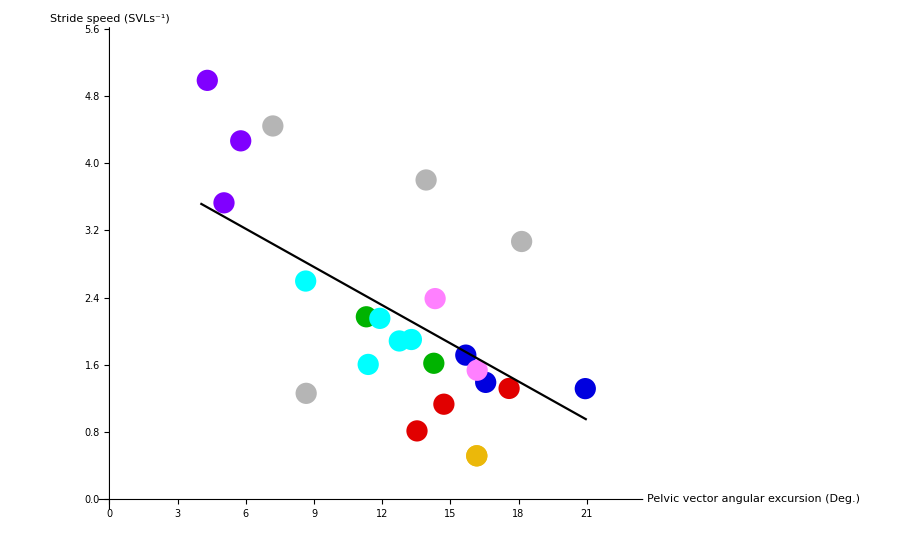

```mathematica
(*Slope and inctercept data from R output*)
Ydata=Table[y=(-0.151324*x)+4.126962,{x,0,23}]; (*Change -0.151324 & 4.126962 based on R stats output*)
Xdata={0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23};
LMElinedata=Thread[{Xdata,Ydata}];
LMEline=ListLinePlot[LMElinedata[[5;;22]],PlotStyle->Black];
SpvPAplot=Show[PEvSSdat,LMEline,ImageSize->900]
```

```mathematica
(*************************************)
```

```mathematica
(*TMT*)

Animal0HGTMTvPelvicexcursion=Thread[{Animal0PelvicAngularExcursions,Animal0TMTHypotheticalGains}];
Animal1HGTMTvPelvicexcursion=Thread[{Animal1PelvicAngularExcursions,Animal1TMTHypotheticalGains}];
Animal2HGTMTvPelvicexcursion=Thread[{Animal2PelvicAngularExcursions,Animal2TMTHypotheticalGains}];
Animal3HGTMTvPelvicexcursion=Thread[{Animal3PelvicAngularExcursions,Animal3TMTHypotheticalGains}];
Animal4HGTMTvPelvicexcursion=Thread[{Animal4PelvicAngularExcursions,Animal4TMTHypotheticalGains}];
Animal5HGTMTvPelvicexcursion=Thread[{Animal5PelvicAngularExcursions,Animal5TMTHypotheticalGains}];
Animal6HGTMTvPelvicexcursion=Thread[{Animal6PelvicAngularExcursions,Animal6TMTHypotheticalGains}];
Animal7HGTMTvPelvicexcursion=Thread[{Animal7PelvicAngularExcursions,Animal7TMTHypotheticalGains}];
HGTMTvPelvicexcursion=Thread[{PelvicAngularExcursionAllAnimals,TMTHypotheticalGainAllAnimals}];

Animal0HGTMTvPelvicexcursionplot=ListPlot[Animal0HGTMTvPelvicexcursion,PlotStyle->{Setting[0.9215686274509803],PointSize->0.017},PlotRange->{{0,23},{0,8}},AxesLabel->{"","TMT"},AxesStyle->Directive[Black,30],LabelStyle->Directive[{Bold,Black,FontFamily->"Calibri"}]];
Animal1HGTMTvPelvicexcursionplot=ListPlot[Animal1HGTMTvPelvicexcursion,PlotStyle->{Setting[0.8823529411764706],PointSize->0.017}];
Animal2HGTMTvPelvicexcursionplot=ListPlot[Animal2HGTMTvPelvicexcursion,PlotStyle->{Setting[0.],PointSize->0.017}];
Animal3HGTMTvPelvicexcursionplot=ListPlot[Animal3HGTMTvPelvicexcursion,PlotStyle->{Setting[0.],PointSize->0.017}];
Animal4HGTMTvPelvicexcursionplot=ListPlot[Animal4HGTMTvPelvicexcursion,PlotStyle->{Setting[0.],PointSize->0.017}];
Animal5HGTMTvPelvicexcursionplot=ListPlot[Animal5HGTMTvPelvicexcursion,PlotStyle->{Setting[0.5019607843137255],PointSize->0.017}];
Animal6HGTMTvPelvicexcursionplot=ListPlot[Animal6HGTMTvPelvicexcursion,PlotStyle->{Setting[1.],PointSize->0.017}];
Animal7HGTMTvPelvicexcursionplot=ListPlot[Animal7HGTMTvPelvicexcursion,PlotStyle->{Setting[0.6941176470588235],PointSize->0.017}];
HGTMTvPelvicexcursionplot=ListPlot[HGTMTvPelvicexcursion,PlotStyle->Black];
```

```mathematica
(*TMTgain v angle*)
TMTHGvPEdat=Show[Animal0HGTMTvPelvicexcursionplot,Animal1HGTMTvPelvicexcursionplot,Animal2HGTMTvPelvicexcursionplot,Animal3HGTMTvPelvicexcursionplot,Animal4HGTMTvPelvicexcursionplot,Animal5HGTMTvPelvicexcursionplot,Animal6HGTMTvPelvicexcursionplot,Animal7HGTMTvPelvicexcursionplot];
```

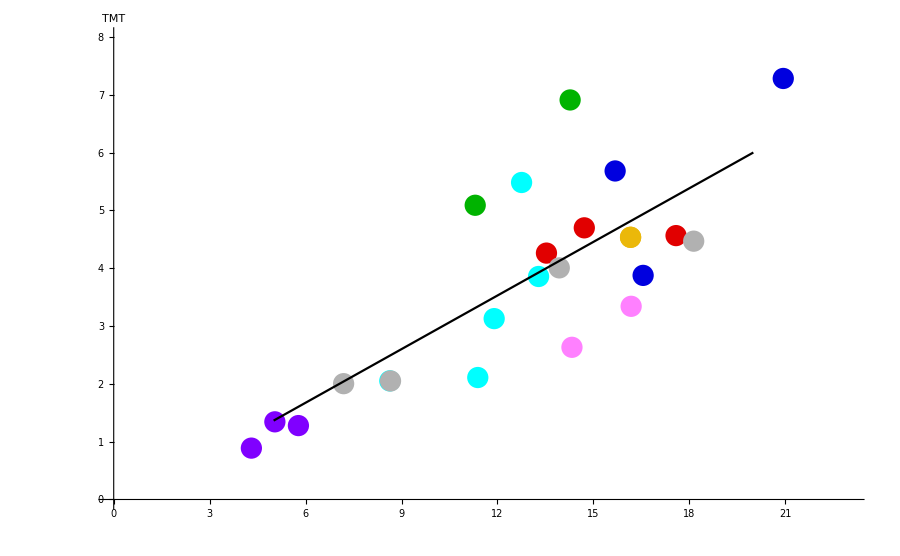

```mathematica
(*Slope and inctercept data from R output*)
Ydata=Table[y=(0.3091854*x)+-0.1811828,{x,0,23}]; (*Change 0.3091854 & -0.1811828 baed on R stats output*)
Xdata={0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23};
LMElinedata1=Thread[{Xdata,Ydata}];
LMEline1=ListLinePlot[LMElinedata1[[6;;21]],PlotStyle->Black];
TvPAplot=Show[TMTHGvPEdat,LMEline1,ImageSize->900]
```

```mathematica
(*************************************)
```

```mathematica
(*ANK*)

Animal0HGANKvPelvicexcursion=Thread[{Animal0PelvicAngularExcursions,Animal0ANKHypotheticalGains}];
Animal1HGANKvPelvicexcursion=Thread[{Animal1PelvicAngularExcursions,Animal1ANKHypotheticalGains}];
Animal2HGANKvPelvicexcursion=Thread[{Animal2PelvicAngularExcursions,Animal2ANKHypotheticalGains}];
Animal3HGANKvPelvicexcursion=Thread[{Animal3PelvicAngularExcursions,Animal3ANKHypotheticalGains}];
Animal4HGANKvPelvicexcursion=Thread[{Animal4PelvicAngularExcursions,Animal4ANKHypotheticalGains}];
Animal5HGANKvPelvicexcursion=Thread[{Animal5PelvicAngularExcursions,Animal5ANKHypotheticalGains}];
Animal6HGANKvPelvicexcursion=Thread[{Animal6PelvicAngularExcursions,Animal6ANKHypotheticalGains}];
Animal7HGANKvPelvicexcursion=Thread[{Animal7PelvicAngularExcursions,Animal7ANKHypotheticalGains}];
HGANKvPelvicexcursion=Thread[{PelvicAngularExcursionAllAnimals,ANKHypotheticalGainAllAnimals}];

Animal0HGANKvPelvicexcursionplot=ListPlot[Animal0HGANKvPelvicexcursion,PlotStyle->{Setting[0.9215686274509803],PointSize->0.017},PlotRange->{{0,23},{0,8}},AxesLabel->{"","Ankle"},AxesStyle->Directive[Black,30],LabelStyle->Directive[{Bold,Black,FontFamily->"Calibri"}]];
Animal1HGANKvPelvicexcursionplot=ListPlot[Animal1HGANKvPelvicexcursion,PlotStyle->{Setting[0.8823529411764706],PointSize->0.017}];
Animal2HGANKvPelvicexcursionplot=ListPlot[Animal2HGANKvPelvicexcursion,PlotStyle->{Setting[0.],PointSize->0.017}];
Animal3HGANKvPelvicexcursionplot=ListPlot[Animal3HGANKvPelvicexcursion,PlotStyle->{Setting[0.],PointSize->0.017}];
Animal4HGANKvPelvicexcursionplot=ListPlot[Animal4HGANKvPelvicexcursion,PlotStyle->{Setting[0.],PointSize->0.017}];
Animal5HGANKvPelvicexcursionplot=ListPlot[Animal5HGANKvPelvicexcursion,PlotStyle->{Setting[0.5019607843137255],PointSize->0.017}];
Animal6HGANKvPelvicexcursionplot=ListPlot[Animal6HGANKvPelvicexcursion,PlotStyle->{Setting[1.],PointSize->0.017}];
Animal7HGANKvPelvicexcursionplot=ListPlot[Animal7HGANKvPelvicexcursion,PlotStyle->{Setting[0.6941176470588235],PointSize->0.017}];
HGANKvPelvicexcursionplot=ListPlot[HGANKvPelvicexcursion,PlotStyle->Black];
```

```mathematica
(*ANKgain v angle*)
ANKHGvPEdat=Show[Animal0HGANKvPelvicexcursionplot,Animal1HGANKvPelvicexcursionplot,Animal2HGANKvPelvicexcursionplot,Animal3HGANKvPelvicexcursionplot,Animal4HGANKvPelvicexcursionplot,Animal5HGANKvPelvicexcursionplot,Animal6HGANKvPelvicexcursionplot,Animal7HGANKvPelvicexcursionplot];
```

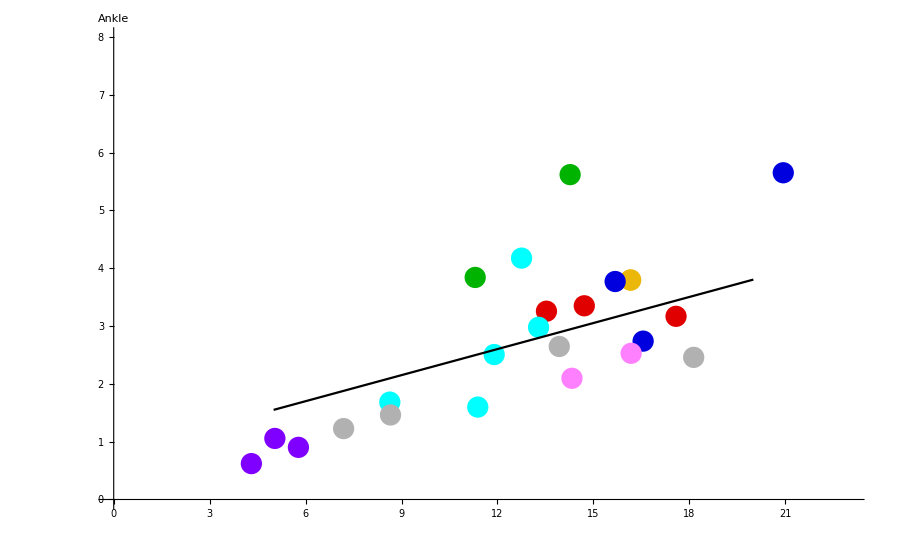

```mathematica
(*Slope and inctercept data from R output*)
Ydata=Table[y=(0.1502582*x)+0.7990194,{x,0,23}]; (*Change 0.1502582 & 0.7990194 based on R stats output*)
Xdata={0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23};
LMElinedata2=Thread[{Xdata,Ydata}];
LMEline2=ListLinePlot[LMElinedata2[[6;;21]],PlotStyle->Black];
AvPAplot=Show[ANKHGvPEdat,LMEline2,ImageSize->900]
```

```mathematica
(*************************************)
```

```mathematica
(*KNE*)

Animal0HGKNEvPelvicexcursion=Thread[{Animal0PelvicAngularExcursions,Animal0KNEHypotheticalGains}];
Animal1HGKNEvPelvicexcursion=Thread[{Animal1PelvicAngularExcursions,Animal1KNEHypotheticalGains}];
Animal2HGKNEvPelvicexcursion=Thread[{Animal2PelvicAngularExcursions,Animal2KNEHypotheticalGains}];
Animal3HGKNEvPelvicexcursion=Thread[{Animal3PelvicAngularExcursions,Animal3KNEHypotheticalGains}];
Animal4HGKNEvPelvicexcursion=Thread[{Animal4PelvicAngularExcursions,Animal4KNEHypotheticalGains}];
Animal5HGKNEvPelvicexcursion=Thread[{Animal5PelvicAngularExcursions,Animal5KNEHypotheticalGains}];
Animal6HGKNEvPelvicexcursion=Thread[{Animal6PelvicAngularExcursions,Animal6KNEHypotheticalGains}];
Animal7HGKNEvPelvicexcursion=Thread[{Animal7PelvicAngularExcursions,Animal7KNEHypotheticalGains}];
HGKNEvPelvicexcursion=Thread[{PelvicAngularExcursionAllAnimals,KNEHypotheticalGainAllAnimals}];

Animal0HGKNEvPelvicexcursionplot=ListPlot[Animal0HGKNEvPelvicexcursion,PlotStyle->{Setting[0.9215686274509803],PointSize->0.017},PlotRange->{{0,23},{0,8}},AxesLabel->{"","Knee"},AxesStyle->Directive[Black,30],LabelStyle->Directive[{Bold,Black,FontFamily->"Calibri"}]];
Animal1HGKNEvPelvicexcursionplot=ListPlot[Animal1HGKNEvPelvicexcursion,PlotStyle->{Setting[0.8823529411764706],PointSize->0.017}];
Animal2HGKNEvPelvicexcursionplot=ListPlot[Animal2HGKNEvPelvicexcursion,PlotStyle->{Setting[0.],PointSize->0.017}];
Animal3HGKNEvPelvicexcursionplot=ListPlot[Animal3HGKNEvPelvicexcursion,PlotStyle->{Setting[0.],PointSize->0.017}];
Animal4HGKNEvPelvicexcursionplot=ListPlot[Animal4HGKNEvPelvicexcursion,PlotStyle->{Setting[0.],PointSize->0.017}];
Animal5HGKNEvPelvicexcursionplot=ListPlot[Animal5HGKNEvPelvicexcursion,PlotStyle->{Setting[0.5019607843137255],PointSize->0.017}];
Animal6HGKNEvPelvicexcursionplot=ListPlot[Animal6HGKNEvPelvicexcursion,PlotStyle->{Setting[1.],PointSize->0.017}];
Animal7HGKNEvPelvicexcursionplot=ListPlot[Animal7HGKNEvPelvicexcursion,PlotStyle->{Setting[0.6941176470588235],PointSize->0.017}];
HGKNEvPelvicexcursionplot=ListPlot[HGKNEvPelvicexcursion,PlotStyle->Black];
```

```mathematica
(*KNEgain v angle*)
KNEHGvPEdat=Show[Animal0HGKNEvPelvicexcursionplot,Animal1HGKNEvPelvicexcursionplot,Animal2HGKNEvPelvicexcursionplot,Animal3HGKNEvPelvicexcursionplot,Animal4HGKNEvPelvicexcursionplot,Animal5HGKNEvPelvicexcursionplot,Animal6HGKNEvPelvicexcursionplot,Animal7HGKNEvPelvicexcursionplot];
```

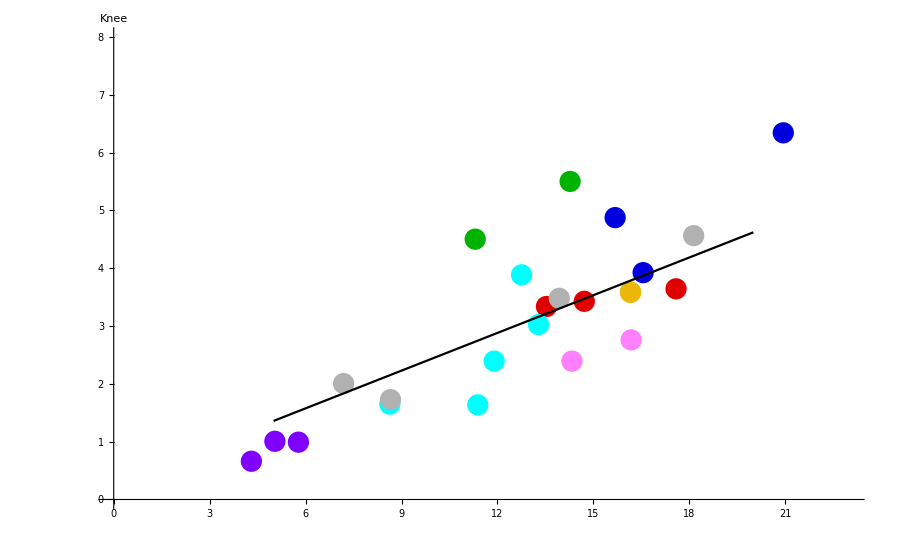

```mathematica
(*Slope and inctercept data from R output*)
Ydata=Table[y=(0.2175045*x)+0.2718847,{x,0,23}]; (*Change 0.2175045 & 0.2718847 based on R stats output*)
Xdata={0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23};
LMElinedata3=Thread[{Xdata,Ydata}];
LMEline3=ListLinePlot[LMElinedata3[[6;;21]],PlotStyle->Black];
KvPAplot=Show[KNEHGvPEdat,LMEline3,ImageSize->900]
```

```mathematica
AllPlots=GraphicsColumn[{TvPAplot,AvPAplot,KvPAplot,SpvPAplot},ImageSize->900];
```

```mathematica
(*********************************************************************************)
(*********************************************************************************)
```

```mathematica
(*Export*)
```

```mathematica
dataDirectory="YOUR DIRECTORY FOR EXPORTED FIGURES";

setpathDataWin=StringJoin[frogworkpath,dataDirectory];(*windows formatted path as string*)
splitpath=FileNameSplit[setpathDataWin,OperatingSystem->"Windows"(*change to MacOSX if necessary*)];
setpathData=FileNameJoin[splitpath,OperatingSystem->os];
SetDirectory[setpathData];

Export["Kinematics Paper - Pelvic angle v Stride speed plot with LME fit.svg",SpvPAplot];
Export["Kinematics Paper - TMT gain v Pelvic angle plot with LME fit.svg",TvPAplot];
Export["Kinematics Paper - Ankle gain v Pelvic angle plot with LME fit.svg",AvPAplot];
Export["Kinematics Paper - Knee gain v Pelvic angle plot with LME fit.svg",KvPAplot];

Print["EXPORTED"]
```

EXPORTED